# Project 2 - Distributions

## Report

Emil Lengman, emillen@kth.se
Simon Enerstrand, simonene@kth.se

## Section. Summary

For this project we were handed a module for randomizing numbers from six different distributions (randomNumber). We are going to use it to test different distribution models, divided in two sub-assignments.

### Section.Subsection Summary sub-assignment 1

#### Description

For this sub-assignment we are going to use the first (index zero in the module) distribution to test three models. We are going to calculate the point estimates for the expected value, and standard deviation, for the random data. Then we are going to determine see which model fits the random data the best. The models are:

pdf(x)∝e^(-a x),x≥0

pdf(x)∝x e^(-a x),x≥0

pdf(x)∝x (x+b)e^(-a x),x≥0

When we’ve found the most fitting model we are going to compute the 95% confidence intervals for the constants in the chosen model.

#### Result

### Section.Subsection Summary sub-assignment 2

#### Description

For this sub-assignment we are going to generate data from all the different distributions and determine which distribution model fits the data the best for each data set (using the  straight line approach). Then we are going to determine the point estimates of the parameters, and compute 95% confidence intervals for those parameters.

#### Result

These are the resulting distribution models for the data (by index in the module):

Exponential distribution

Geometric distribution

Gamma distribution

Normal distribution

Binomial distribution

## Section. Distribution parameters

### Section.Subsection Solution

### Section.Subsection Expected value, and standard deviation

#### Solution

First we will create a list of many random values.Then calculate the expected value, and standard deviation. You can use the following formula to calculate expected value:

x̄=1/n∑_(i=1)^n x_i

To calculate the standard deviation

s=√(1/(n-1)∑_(i=1)^n (x_i-x̄)^2)

Mathematica has built-in function to do that for us, so we used those instead.

#### Code

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
Once[Get["Project2.m","IX1501"]]
```

```mathematica
n =1000;
```

```mathematica
rand = randomNumber[0, n];
```

```mathematica
μ=Mean[rand]
```

5.21291

```mathematica
σ = StandardDeviation[rand]
```

3.56175

### Section.Subsection Trying models

#### Solution

P(Ω) = 1

C*∫_0^∞ pd(x)ⅆx= 1, x > 0

#### Code

##### Model 1

```mathematica
c= c/.NSolve[Integrate[c E^(-a x), {x, 0, ∞}] == 1, c][[1]]
```

ConditionalExpression[a,Re[a]>0]

```mathematica
a = a /. NSolve[{Integrate[x a E^(-a x), {x, 0 , ∞}] == μ && a ≥ 0}, a][[1]]
```

0.191831

```mathematica
pdf[x_] := a * E^(-a x)  (*The model*)
```

```mathematica
sort=Sort[rand];
Δ=1/n;
pdata=Δ/2+Range[0,1-Δ,Δ]//N;
```

#### Discussion

### Section.Subsection Second model

#### Solution

#### Code

### Section.Subsection Third model

#### Solution

#### Code

### Section.Subsection Discussion

## Section. Which distribution?

### Section.Subsection Determine a distribution model

#### Solution

To determine the distribution model of the random data we can use the built-in function FindDistribution, which takes a list of values and returns a distribution. This only works reliably when we use a large enough sample size.

#### Code

##### Distribution 1

```mathematica
ClearAll["`*"]
```

```mathematica
n = 1000;
```

```mathematica
rand = randomNumber[1, n];
μ= Mean[rand];
FindDistribution[rand]
```

ExponentialDistribution[4.43923]

```mathematica
distribution = EstimatedDistribution[rand, ExponentialDistribution[λ]]
```

ExponentialDistribution[4.43923]

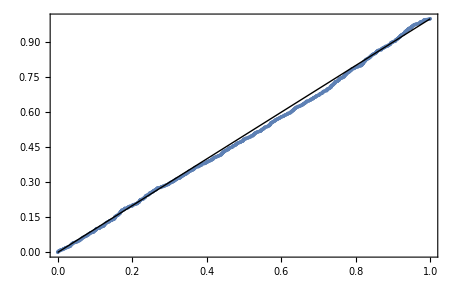

```mathematica
ProbabilityPlot[rand, distribution]
```

##### Distribution 2

```mathematica
ClearAll["`*"]
```

```mathematica
n = 1000;
rand = randomNumber[2, n];
FindDistribution[rand]
```

GeometricDistribution[0.0633593]

GeometricDistribution[0.0633593]

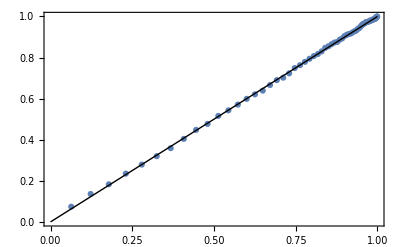

```mathematica
distribution=EstimatedDistribution[rand,GeometricDistribution[p]]
ProbabilityPlot[rand,distribution]
```

##### Distribution 3

```mathematica
ClearAll["`*"]
```

```mathematica
n = 1000;
```

```mathematica
numbers = randomNumber[3, n];
FindDistribution[numbers]
```

GammaDistribution[8.41243,1.50026]

```mathematica
distribution=EstimatedDistribution[numbers,GammaDistribution[α,β]]
```

GammaDistribution[8.39944,1.50893]

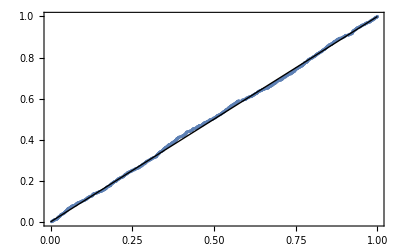

```mathematica
ProbabilityPlot[numbers, distribution]
```

##### Distribution 4

```mathematica
ClearAll["`*"]
```

```mathematica
n = 100;
```

```mathematica
numbers = randomNumber[4, n];
FindDistribution[numbers]
```

NormalDistribution[2.8657,4.88848]

```mathematica
distribution=EstimatedDistribution[numbers, NormalDistribution[μ,σ]]
```

NormalDistribution[2.87948,4.56649]

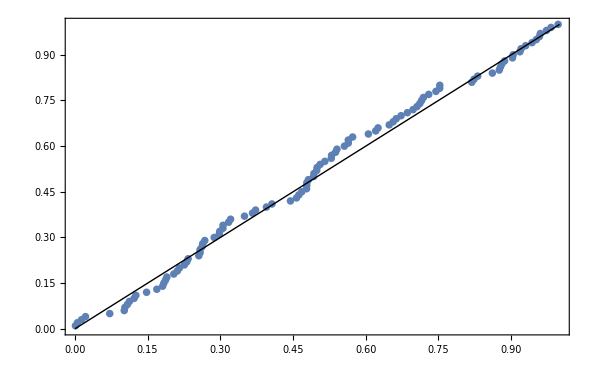

```mathematica
ProbabilityPlot[numbers, distribution]
```

##### Distribution 5

```mathematica
n = 1000;
```

```mathematica
numbers = randomNumber[5, n];
FindDistribution[numbers]
```

BinomialDistribution[15,0.22362]

```mathematica
distribution = EstimatedDistribution[numbers, BinomialDistribution[num, p]]
```

BinomialDistribution[11,0.295545]

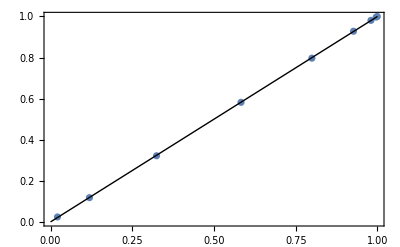

```mathematica
ProbabilityPlot[numbers, distribution]
```

##### Distribution 6

```mathematica
ClearAll["`*"]
```

```mathematica
n = 100;
```

```mathematica
numbers = randomNumber[6, n];
FindDistribution[numbers]
```

PoissonDistribution[9.61765]

```mathematica
distribution = EstimatedDistribution[numbers, PoissonDistribution[μ]]
```

PoissonDistribution[9.57]

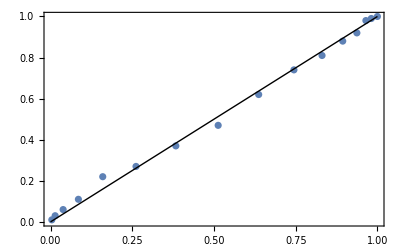

```mathematica
ProbabilityPlot[numbers, distribution]
```

### Section.Subsection Point estimates, and confidence intervals, for parameters

#### Solution

#### Code

##### Distribution 1 (Exponential distribution)

```mathematica
ClearAll["`*"]
```

```mathematica
Needs["HypothesisTesting`"]
```

```mathematica
amountOfLists=100;
```

```mathematica
listLength=1000;
```

```mathematica
matrixOfRands=randomNumber[1,{amountOfLists,listLength}];
```

```mathematica
findλ[data_]:=List@@EstimatedDistribution[data,ExponentialDistribution[λ]];
```

```mathematica
{λlist}=Transpose[findλ/@matrixOfRands];
```

```mathematica
confλ=MeanCI[λlist, ConfidenceLevel->0.95]
```

{4.4634,4.51706}

```mathematica
(* WALLA BRUSH HÄR MÅSTE DU SE TILL ATT DET DÄR MED 10% ÄR GREJS, TACK MR *)
```

##### Distribution 2 (Geometric distribution)

```mathematica
ClearAll["`*"]
```

```mathematica
amountOfLists=100;
```

```mathematica
listLength=1000;
```

```mathematica
matrixOfRands=randomNumber[2,{amountOfLists,listLength}];
```

```mathematica
findp[data_]:=List@@EstimatedDistribution[data,GeometricDistribution[p]]
```

```mathematica
{prob}=Transpose[findp/@matrixOfRands];
```

```mathematica
confp=MeanCI[prob, ConfidenceLevel->0.95]
```

{0.0640976,0.0649245}

```mathematica
(* WALLA BRUSH HÄR MÅSTE DU SE TILL ATT DET DÄR MED 10% ÄR GREJS, TACK MR *)
```

##### Distribution 3 (Gamma distribution)

```mathematica
ClearAll["`*"]
```

```mathematica
amountOfLists=100;
```

```mathematica
listLength=1000;
```

```mathematica
matrixOfRands=randomNumber[3,{amountOfLists,listLength}];
```

```mathematica
findαandβ[data_]:=List@@EstimatedDistribution[data,GammaDistribution[α,β]]
```

```mathematica
{αlist,βlist}=Transpose[findαandβ/@matrixOfRands];
```

```mathematica
confα=MeanCI[αlist, ConfidenceLevel->0.95]
```

{7.93034,8.06663}

```mathematica
confβ=MeanCI[βlist, ConfidenceLevel->0.95]
```

{1.58849,1.61571}

```mathematica
(* WALLA BRUSH HÄR MÅSTE DU SE TILL ATT DET DÄR MED 10% ÄR GREJS, TACK MR *)
```

##### Distribution 4 (Normal distribution)

```mathematica
ClearAll["`*"]
```

```mathematica
amountOfLists=100;
```

```mathematica
listLength=1000;
```

```mathematica
matrixOfRands=randomNumber[4,{amountOfLists,listLength}];
```

```mathematica
findμandσ[data_]:=List@@EstimatedDistribution[data,NormalDistribution[μ, σ]]
```

```mathematica
{μlist,σlist}=Transpose[findμandσ/@matrixOfRands];
```

```mathematica
confμ = MeanCI[μlist, ConfidenceLevel->0.95]
```

{2.9924,3.05406}

```mathematica
confσ = MeanCI[σlist, ConfidenceLevel->0.95]
```

{4.98615,5.02915}

```mathematica
(* WALLA BRUSH HÄR MÅSTE DU SE TILL ATT DET DÄR MED 10% ÄR GREJS, TACK MR *)
```

##### Distribution 5 (Binomial distribution)

```mathematica
ClearAll["`*"]
```

```mathematica
amountOfLists=100;
```

```mathematica
listLength=1000;
```

```mathematica
matrixOfRands=randomNumber[5,{amountOfLists,listLength}];
```

```mathematica
findmandp[data_]:=List@@EstimatedDistribution[data,BinomialDistribution[listLength ,p]]
```

```mathematica
{m, plist}=Transpose[findmandp/@matrixOfRands];
```

```mathematica
confp=MeanCI[plist, ConfidenceLevel->0.95]
```

{0.00329019,0.00330865}

```mathematica
(* WALLA BRUSH HÄR MÅSTE DU SE TILL ATT DET DÄR MED 10% ÄR GREJS, TACK MR *)
```

##### Distribution 6 (Poisson distribution)

```mathematica
amountOfLists=100;
```

```mathematica
listLength=1000;
```

```mathematica
matrixOfRands=randomNumber[6,{amountOfLists,listLength}];
```

```mathematica
List@@EstimatedDistribution[randomNumber[6, 100],PoissonDistribution[μ]]
```

{9.8}

```mathematica
findμ[data_]:=List@@EstimatedDistribution[data,PoissonDistribution[μ]]
```

```mathematica
μlist=Transpose[findμ/@matrixOfRands][[1]];
```

```mathematica
confμ=MeanCI[μlist, ConfidenceLevel->0.95]
```

{9.7916,9.82754}

```mathematica
(* WALLA BRUSH HÄR MÅSTE DU SE TILL ATT DET DÄR MED 10% ÄR GREJS, TACK MR *)
```